```mathematica
ln[w]=Log[1+w]
A[q_,w_]=(q w ln[w] (4 w-(w+3) ln[w])+4 w^2-4 w ln[w]+(1-w)ln[w]^2)/(w (q+1) (q w+1) ln[w])
```

Log[1+w]

(4 w^2-4 w Log[1+w]+(1-w) Log[1+w]^2+q w Log[1+w] (4 w-(3+w) Log[1+w]))/((1+q) w (1+q w) Log[1+w])

```mathematica
Plot3D[q A[q,w],{q,0,2},{w,0,10},AxesLabel->{q,w},PlotRange->All]
```

-Graphics3D-

```mathematica
N[A[2,2]]
```

0.516432

```mathematica
N[2000 A[2000,2]]
```

1.25321

```mathematica
Plot3D[A[q,w],{q,0,100},{w,0,1000},AxesLabel->{q,w},PlotRange->All]
```

-Graphics3D-

```mathematica
D[A[q,w],w]
```

((1-w)/(w (1+w))+q (4-(3+w)/(1+w)-Log[1+w])-(4 w)/((1+w) Log[1+w]^2)+4/Log[1+w]-((1-w) Log[1+w])/w^2-Log[1+w]/w)/((1+q) (1+q w))-(q (-4+(4 w)/Log[1+w]+((1-w) Log[1+w])/w+q (4 w-(3+w) Log[1+w])))/((1+q) (1+q w)^2)

```mathematica
Solve[D[A[q,w],w]≥0&&q>0&&w>0,{q,w},Reals]
```

$Aborted

```mathematica
Solve[A[q,w]>1/q&&q>0&&w>0,q]
```

Solve::cpow: Solve was unable to prove that a radical of an expression containing only real variables and parameters is real valued. If you are interested only in solutions for which all radicals contained in the input are real valued, use Solve with domain argument Reals.

```mathematica
Solve[(-4+(4 w)/Log[1+w]+((1-w) Log[1+w])/w+q (4 w-(3+w) Log[1+w]))/((1+q) (1+q w))>1/q&&q>0&&w>0,q,Reals]
```

Solve::fdimc: When parameter values satisfy the condition 1 < w < Root[{3\ Log[« 1 »] - 3\ Slot[« 1 »] + Log[« 1 »]\ Slot[« 1 »] &, 7.5773567925986795089}] || 0 < w < 1, the solution set contains a full-dimensional component; use Reduce for complete solution information.

{}

```mathematica
B[_q]=Min
```

```mathematica
res=NDSolveValue[{p''[x]==p'[x]^2 A[2 p[x]-1,1],p'[0]==0.1,p[0]==1},p,{x,0,100}]
```

InterpolatingFunction[{{0., 100.}}, <>]

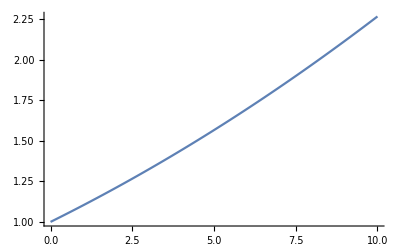

```mathematica
Plot[res[x],{x,0,10}]
```

```mathematica
Simplify[A[2 p[x]-1,0.1],p[x]==1/2]
```

1.05462

```mathematica
Clear["Global`*"]
```